Arithmetic

```mathematica
2+2
```

4

```mathematica
2^20
```

1048576

```mathematica
20! (*factorial*)
```

2432902008176640000

#### Functions

```mathematica
Plus[2,2](*addition*)
```

4

```mathematica
Times[2,20](*multiplication*)
```

40

```mathematica
Max[2,20](*maximun of given numbers*)
```

20

```mathematica
RandomInteger[10] (* random integer between 0 and 10*)
```

8

```mathematica
Power[3,2](*power of a^b*)
```

9

```mathematica
RandomReal[] (*gives random number between 0 and 1*)
```

0.492107

```mathematica
Framed[{1,2,3}](*puts frame around the value*)
```

{1,2,3}

#### Lists

```mathematica
{1,2,3,4,5}(*defines an list*)
```

{1,2,3,4,5}

```mathematica
Max[{1,2,3,4,5}](*gives maximun from a list*)
```

5

```mathematica
Range[10](*generates list till number given*)
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Reverse[Range[10]](*reverses the list generated by range[], output of range[] is input to reverse[]*)
```

{10,9,8,7,6,5,4,3,2,1}

```mathematica
Join[{1,2,3,4},{5,6,7,8}](*joins to list*)
```

{1,2,3,4,5,6,7,8}

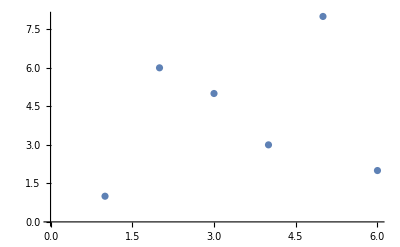

```mathematica
ListPlot[{1,6,5,3,8,2}](*plot list points*)
```

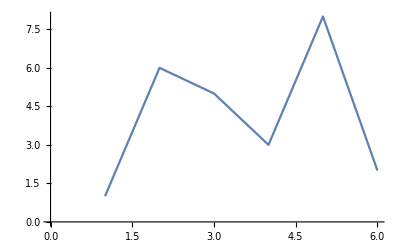

```mathematica
ListLinePlot[{1,6,5,3,8,2}](*plot list points and joins them*)
```

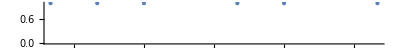

```mathematica
NumberLinePlot[{1,6,5,3,8,2}](*plot points on a numberline*)
```

```mathematica
Column[{1,6,5,3,8,2}](* column[] stacks the list verticaly*)
```

1
6
5
3
8
2

```mathematica
{1,2,3}+10(*list arithmetic, same for all operators*)
```

{11,12,13}

```mathematica
Length[Range[15]](*length of list generated by range[]*)
```

15

```mathematica
Total[Range[10]](*Total of all elements of a list*)
```

55

```mathematica
Sort[{7,4,2,9,0,4,6,2,5,7}](*sort list in ascending order*)
```

{0,2,2,4,4,5,6,7,7,9}

```mathematica
Part[{1,3,5,6,2},4](*picks 4th element of a list*)
```

6

```mathematica
{a,b,c,d,e,f,g}[[2]](*another way to part from list*)
```

b

```mathematica
{a,b,c,d,e,f,g}[[{2,4,5}]](*part multiple values*)
```

{b,d,e}

```mathematica
Take[{1,6,3,8,6,2,7},5](*takes first 5 elements of a list*)
```

{1,6,3,8,6}

```mathematica
Table[n^2,{n,1,10}](*generates list of squares till 10*)
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Table[Column[Range[n]],{n,8}](*table of column of list*)
```

{1,1
2,1
2
3,1
2
3
4,1
2
3
4
5,1
2
3
4
5
6,1
2
3
4
5
6
7,1
2
3
4
5
6
7
8}

```mathematica
Grid[Table[x,4,5]](*generates grid from a list, array*)
```

x | x | x | x | x
x | x | x | x | x
x | x | x | x | x
x | x | x | x | x

```mathematica
Transpose[{{1,2},{3,4},{5,6},{7,8},{9,10}}](*rearranges lists*)
```

{{1,3,5,7,9},{2,4,6,8,10}}

### Language Constructs

```mathematica
a = 12(*variables*)
```

12

```mathematica
%(*recent output*)
```

12

```mathematica
f[x_]= x^2(*defines function, x_ is pattern*)
```

x^2

```mathematica
f[4]
```

16

```mathematica
ColorNegate@Red(*use @ to apply function to values*)
```

RGBColor[0., 1., 1.]

```mathematica
Hue/@{0.1,0.2,0.3,0.4}(*applies to list elements*)
```

{Hue[0.1],Hue[0.2],Hue[0.3],Hue[0.4]}

```mathematica
-Graphics-//EdgeDetect//ColorNegate(*apply EdgeDetect[] as an after thought*)
```

-Graphics-

```mathematica
Blur[#,5]&/@{-Graphics-,-Graphics-,-Graphics-}(*anonymous functions*)
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
NestList[Framed,x,5](*using framed as recursive function*)
```

{x,x,x,x,x,x}

```mathematica
If[2+2==4,x,y](*conditional, If[expr,then,else]*)
```

x

```mathematica
Cases[{{1,RGBColor[1, 0, 0]},{1,RGBColor[0, 0, 1]},{1,RGBColor[1, 0, 0],RGBColor[0, 0, 1]},{2,RGBColor[0, 1, 0],RGBColor[0, 0, 1]},{2,RGBColor[0, 0, 1]}},{_,_}](*picks the element that match the pattern, _ single value, __ sequence of vlues*)
```

{{1,RGBColor[1, 0, 0]},{1,RGBColor[0, 0, 1]},{2,RGBColor[0, 0, 1]}}

```mathematica
Counts[{a,a,b,c,a,a,b,c,c,a,a}](*creates a hash map*)
```

<|12→6,b→2,c→3|>

```mathematica
bin=CreateDatabin[ ](*creates a wolfram data drop*)
```

Databin[…]

```mathematica
DatabinAdd[bin,{1,2,3,4}](*drop data into bin*)
```

Databin[…]

```mathematica
Import["http://un.org"](*importing data from external sources*)
```

مرحبا بكم في موقع الأمم المتحدة    
 

欢迎来到联合国网站
   
 

Welcome to the United Nations website    
 

Bienvenue sur le site Internet des Nations Unies    
 

Добро пожаловать в ООН!    
 

Bienvenido al sitio web de las Naciones Unidas      
 
 
 
      
 
 
 

مرحبا بكم في موقع الأمم المتحدة    
 

欢迎来到联合国网站
   
 

Welcome to the United Nations website    
 

Bienvenue sur le site Internet des Nations Unies    
 

Добро пожаловать в ООН!    
 

Bienvenido al sitio web de las Naciones Unidas          
 
 
  
 
  
    
  عربي     中文     English     Français     Русский     Español

```mathematica
Import["http://wikipedia.org","Images"](*import images from external source*)
```

{-Graphics-,-Graphics-}

#### Colors

```mathematica
Red(*gives red swatch*)
```

RGBColor[1, 0, 0]

```mathematica
{Red,Blue,Magenta}(*list of colors*)
```

{RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[1, 0, 1]}

```mathematica
ColorNegate[Blue](*negates the color*)
```

RGBColor[1., 1., 0.]

```mathematica
RGBColor[1,0.5,0](*specifies color in RGB format*)
```

RGBColor[1, 0.5, 0]

```mathematica
Hue[0.3](*specify color in Hue*)
```

Hue[0.3]

```mathematica
Blend[{Magenta,Purple}](*blend colors together*)
```

RGBColor[0.75, 0, 0.75]

```mathematica
RandomColor[](*gives random color*)
```

RGBColor[0.9339543948529283, 0.6702663667413926, 0.11220642726793773]

```mathematica
Style["A",Red](*styles letter A with red*)
```

A

#### Graphics



```mathematica
Graphics[Disk[]](*generates graphics Disk*)
```

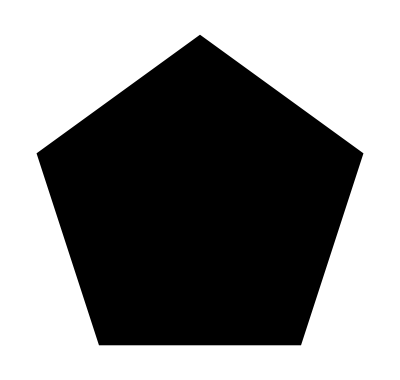

```mathematica
Graphics[RegularPolygon[5]](*regular polygon of sides 5*)
```

```mathematica
Graphics3D[Sphere[]](*generates sphere*)
```

-Graphics3D-

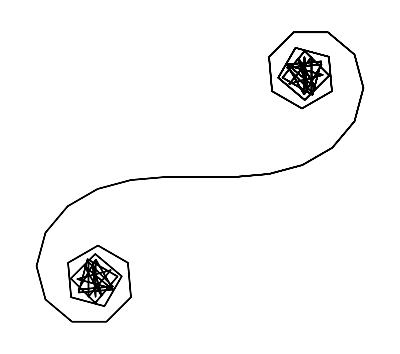

```mathematica
Graphics[Line[AnglePath[Table[n*5°,{n,200}]]]](*gives path by turning speciic angles*)
```

#### Images

```mathematica
CurrentImage[](*gives current image from webcam*)
```

-Graphics-

```mathematica
Blur[CurrentImage[]](*blur the image*)
```

-Graphics-

```mathematica
EdgeDetect[CurrentImage[]](*edge detect the image*)
```

-Graphics-

```mathematica
DominantColors[CurrentImage[]](*extract the dominant colors*)
```

{RGBColor[0.01346772535573807, 0.002750650578962002, 0.0028006450558304232],RGBColor[0.20362712600788585, 0.1712114689130018, 0.11205739138427914],RGBColor[0.5207174760945269, 0.506938571430901, 0.48759922311235854],RGBColor[0.9806182613879734, 0.9814230900669493, 0.9770022535150261],RGBColor[0.6554466423665369, 0.5065293473947686, 0.39171203953915407],RGBColor[0.8853843223919957, 0.7237576069722559, 0.5831619055625439]}

```mathematica
Binarize[CurrentImage[]](*binarize the image or apply threshold*)
```

-Graphics-

```mathematica
Rasterize["WOLFRAM"](*converts text into images*)
```

-Graphics-

#### Strings

```mathematica
StringLength["hello"](*gets length of string*)
```

5

```mathematica
StringTake["Machine Learning",5](*takes first 5 of string*)
```

Machi

```mathematica
Characters["Machine Learning"](*split string into characters*)
```

{M,a,c,h,i,n,e, ,L,e,a,r,n,i,n,g}

```mathematica
TextWords["The language it uses is known as Wolfram Language"](*slpits into words*)
```

{The,language,it,uses,is,known,as,Wolfram,Language}

```mathematica
TextSentences["Wolfram Language is a multi-paradigm symbolic language similar to LISP, meaning code and data are alike. You can manipulate the code the same way you do for data and this makes language very powerfull. It is a high level language higher than most mainstream languages. There are builtin functions for almost everything ranging from geography to linguistics to audio"](*split text into sentences*)
```

{Wolfram Language is a multi-paradigm symbolic language similar to LISP, meaning code and data are alike.,You can manipulate the code the same way you do for data and this makes language very powerfull.,It is a high level language higher than most mainstream languages.,There are builtin functions for almost everything ranging from geography to linguistics to audio}

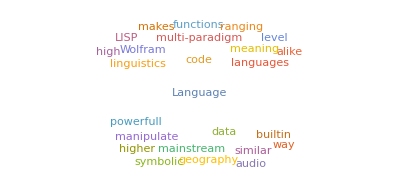

```mathematica
WordCloud["Wolfram Language is a multi-paradigm symbolic language similar to LISP, meaning code and data are alike. You can manipulate the code the same way you do for data and this makes language very powerfull. It is a high level language higher than most mainstream languages. There are builtin functions for almost everything ranging from geography to linguistics to audio"](*generates word cloud*)
```

#### Knowledge

```mathematica
Entity["Species","Species:FelisCatus"][EntityProperty["Species","Image"]](*use ctrl+= to specify input in natural language*)
```

-Graphics-

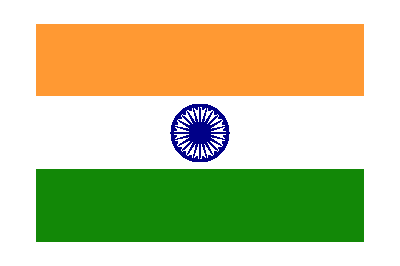

```mathematica
Entity["Country","India"]["Flag"](*gets flag of a country*)
```

```mathematica
EntityList[EntityClass["Planet",All]](*gets list from natural language input*)
```

{Mercury,Venus,Earth,Mars,Jupiter,Saturn,Uranus,Neptune}

```mathematica
Entity["Artwork","TheLastSupper::LeonardoDaVinci"]["Image"]
```

-Graphics-

```mathematica
Entity["Chemical","Benzene"]["MoleculePlot"](*gets molecular plot of the chemical*)
```

-Graphics3D-

```mathematica
Entity["AnatomicalStructure","Skull"]["Graphics3D"](*3D of human skull*)
```

-Graphics3D-

```mathematica
Quantity[30, "Miles"](*use units in computation*)
```

30 mi

```mathematica
UnitConvert[Quantity[2.6, "Hours"],"Minutes"](*converts one unit to another*)
```

156. min

```mathematica
CurrencyConvert[LinguisticAssistant,LinguisticAssistant](*converts one currency to another*)
```

105.80 $

```mathematica
GeoListPlot[{LinguisticAssistant,LinguisticAssistant,LinguisticAssistant}](*ploting countries on world map*)
```

-Graphics-

#### Visualization

```mathematica
ListPlot[{1,6,5,3,8,2}](*plot list points*)
```

-Graphics-

```mathematica
ListLinePlot[{1,6,5,3,8,2}](*plot list points and joins them*)
```

-Graphics-

```mathematica
PieChart[{1,5,7,3}](*generates pie chart from list*)
```

-Graphics-

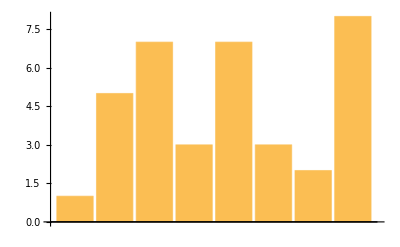

```mathematica
BarChart[{1,5,7,3,7,3,2,8}](*generates bar chart from list*)
```

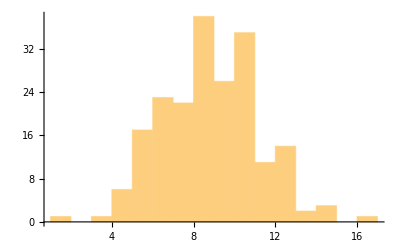

```mathematica
Histogram[StringLength[Take[WordList[ ],200]]](*generates histogram of the common words*)
```

```mathematica
ListPlot3D[GeoElevationData[GeoDisk[ LinguisticAssistant  ,Quantity[10, "Miles"]]]](*3d surface*)(*not working on my internet connection*)
```

```mathematica
ListContourPlot[GeoElevationData[GeoDisk[ LinguisticAssistant  ,Quantity[10, "Miles"]]]](*contours of the elevation data*)(*not working on my internet connection*)
```

```mathematica
ReliefPlot[GeoElevationData[GeoDisk[ LinguisticAssistant  ,Quantity[100, "Miles"]]]](*2d plot, colors according to the values*)(*not working on my internet connection*)
```

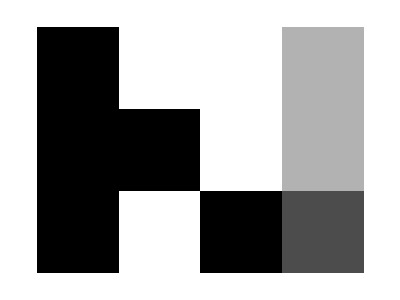

```mathematica
ArrayPlot[{{1,0,0,0.3},{1,1,0,0.3},{1,0,1,0.7}}](*ploting from arrays*)
```

#### Interactive

```mathematica
Manipulate[Style[x,200,Pink],{x,1,20}](*create a live interactive form*)
```

```mathematica
CloudDeploy[GeoGraphics[GeoRange -> All, GeoProjection -> "Albers"]](*deploying to wolfram cloud*)
```

CloudObject[]